```mathematica
dist=NormalDistribution[0.05,0.10]
```

NormalDistribution[0.05,0.1]

```mathematica
1-CDF[dist,0.10]
```

0.308538

```mathematica
CDF[dist,0.15]-CDF[dist,-0.05]
```

0.682689

```mathematica
Quantile[dist,0.01]
```

-0.182635

```mathematica
Quantile[dist,0.05]
```

-0.114485

```mathematica
Quantile[dist,0.95]
```

0.214485

```mathematica
Quantile[dist,0.99]
```

0.282635

```mathematica
msft=NormalDistribution[0.05,0.10]
sbux=NormalDistribution[0.025,0.05]
```

NormalDistribution[0.05,0.1]

NormalDistribution[0.025,0.05]

```mathematica
r=NormalDistribution[0.04,0.09]
```

NormalDistribution[0.04,0.09]

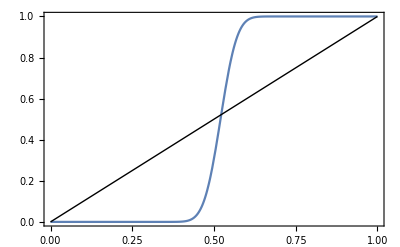

```mathematica
ProbabilityPlot[msft]
```

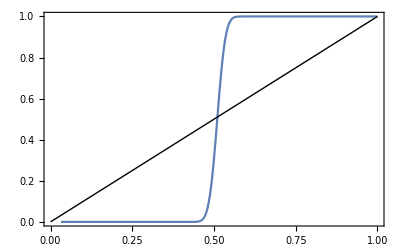

```mathematica
ProbabilityPlot[sbux]
```

```mathematica
range=Range[-0.25,0.35,0.01];
```

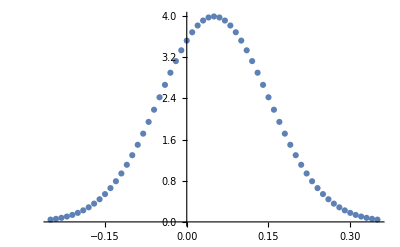

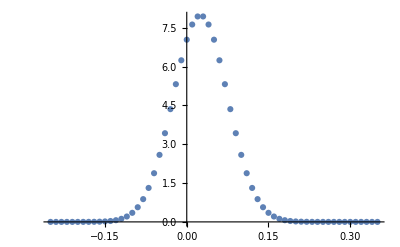

```mathematica
ListPlot[Transpose[{range,PDF[msft,#]&/@range}]]
ListPlot[Transpose[{range,PDF[sbux,#]&/@range}]]
```

```mathematica
dist=NormalDistribution[10500,1000]
```

NormalDistribution[10500,1000]

```mathematica
N@CDF[dist,9000]
```

0.0668072

```mathematica
CDF[dist,10500]
Quantile[dist,0.05]
```

1/2

8855.15

```mathematica
8855.146373048527/10000-1
```

-0.114485

```mathematica
CDF[msft,0.05]
Quantile[msft,0.05]
CDF[msft,-0.1]
```

0.5

-0.114485

0.0668072